```mathematica
(*
Characteristic polynomial of the system in closed loop with a PDmu controller
*)
```

```mathematica
Δ[s_,kp_,kd_,μ_]:= Sqrt[s^2+1]+kp+kd s^μ
```

```mathematica
(*
Stability crossing curve for w = 0
*)
```

```mathematica
Solve[Δ[0, kp, kd, μ]==0, kp]
```

{{kp→-1-0^μ kd}}

```mathematica
(*
Computing kp(w) and kd(w)
*)
```

```mathematica
FullSimplify[Solve[ComplexExpand[Re[Δ[I*w,kp,kd,mu]]==0 && ComplexExpand[Im[Δ[I*w,kp,kd,mu]]]==0],{kp,kd}]]
```

{{kp→((-1+w^2)^2)^(1/4) (-Cos[1/2 Arg[1-w^2]]+((w^2)^(mu/2) Cot[mu Arg[ⅈ w]] Sin[1/2 Arg[1-w^2]])/(√((w^4)^(mu/2)))),kd→-(((-1+w^2)^2)^(1/4) Csc[mu Arg[ⅈ w]] Sin[1/2 Arg[1-w^2]])/(√((w^4)^(mu/2)))}}

```mathematica
kpp[w_, mu_]:=((-1+w^2)^2)^(1/4) (-Cos[1/2 Arg[1-w^2]]+((w^2)^(mu/2) Cot[mu Arg[ⅈ w]] Sin[1/2 Arg[1-w^2]])/(√((w^4)^(mu/2))))
```

```mathematica
kdd[w_, mu_]:=-(((-1+w^2)^2)^(1/4) Csc[mu Arg[ⅈ w]] Sin[1/2 Arg[1-w^2]])/(√((w^4)^(mu/2)))
```

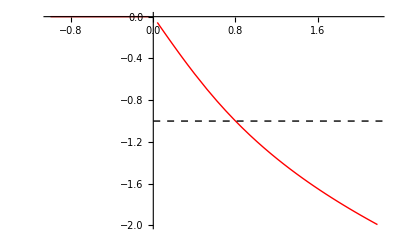

```mathematica
P1 =ParametricPlot[{kpp[w, 0.5], kdd[w, 0.5]}, {w, 0, 2.4}, PlotStyle->{Red, Thick}];
P2 = Plot[-1,{kd0, 0, 10}, PlotStyle->{Black,  Dashed, Thick} ];
Show[P1, P2]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ToMatlab.m
f=OpenWrite["funciones_2nd_ex.m"];
WriteMatlab[kpp[w, mu],f,"kp"];
WriteMatlab[kdd[w, mu],f,"kd"];
Close[f];
```